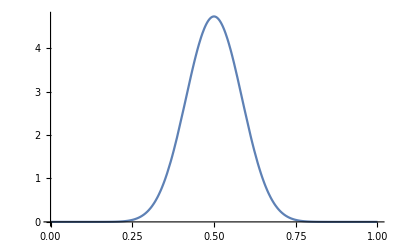

```mathematica
Plot[12*Evaluate[PDF[UniformSumDistribution[12],x] /. {x -> y*12}], {y,0,1}]
```

```mathematica
t1 = TransformedDistribution[U^(1/3),U \[Distributed] UniformDistribution[]]
```

BetaDistribution[3,1]

```mathematica
tf=TransformedDistribution[A+B,{A\[Distributed]t1,B\[Distributed]t1}]
```

TransformedDistribution[x1+x2,{x1\[Distributed]BetaDistribution[3,1],x2\[Distributed]BetaDistribution[3,1]}]

```mathematica
ee= PDF[tf]
```

Function[x,Piecewise[{{(3 x^5)/10, 0<x≤1}, {18/5-9 x+6 x^2-(3 x^5)/10, 1<x<2}, {0, True}}],Listable]

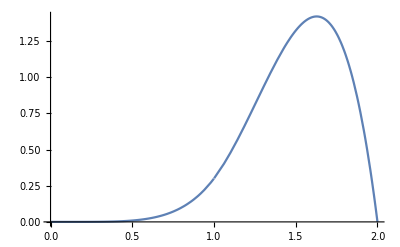

```mathematica
Plot[ee[x],{x,0,2}]
```

```mathematica
MomentGeneratingFunction[LogisticDistribution,t]
```

MomentGeneratingFunction[LogisticDistribution,t]

```mathematica
Evaluate[%]
```

```mathematica
MomentGeneratingFunction[LogisticDistribution[],t]
```

1/Sinc[π t]

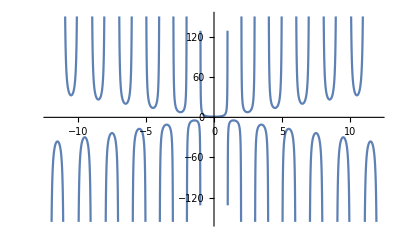

```mathematica
Plot[1/Sinc[π t],{t,-12.,12.}]
```

```mathematica
PDF[LogisticDistribution[],x]
```

ⅇ^-x/((1+ⅇ^-x)^2)

```mathematica
Sinc
```

```mathematica
Beta
```

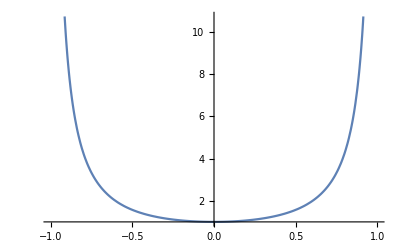

```mathematica
Plot[Beta[1+t,1-t], {t,-1,1}]
```